## Question 5

```mathematica
Clear["Global`*"]
```

```mathematica
g = 9.81;
```

```mathematica
xmax[k_,vv_] := (v=vv;tfinal[theta_] :=

(    sol=  

NDSolve [ { x''[t] == -k x'[t]Sqrt[y'[t]^2 + x'[t]^2] , y''[t] == -k y'[t]Sqrt[y'[t]^2 + x'[t]^2] -g,x[0] == 0, y[0] == 0, x'[0] == v Cos[theta],y'[0] == v Sin[theta] }, {x, y}, {t, 0, 10}] ;

 yy[t_] = y[t] /. sol[[1]]; xx[t_] = x[t] /. sol[[1]];  t/.  FindRoot[ yy[t] , {t, 1, 10}, MaxIterations -> 50]    );

  xfinal[theta_?NumericQ] := xx[tfinal[theta]];

 FindMaximum[xfinal[theta], {theta, 0.1, 1.3}][[1]])
```

## Part A

```mathematica
{xmax[.4,50], v^2/g}
```

{7.27249,254.842}

## Part B

```mathematica
Plot[{xmax[.4,v],xmax[.2,v],xmax[0,v]},{v,0,50},PlotRange->{0,20}];
```

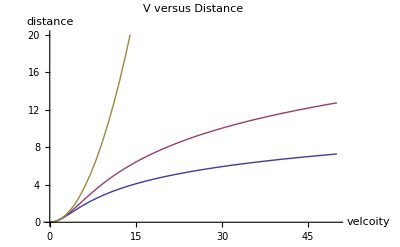

```mathematica
Show[%69,PlotLabel->"V versus Distance",AxesLabel->{"velcoity","distance"}]
```

The yellow line is  no friction, the magenta half the friction, and the blue the friction = .4